```mathematica
BlueC=RGBColor[0.2627,0.4313,1];
PurpleC=RGBColor[0.5411,0.0784,0.9607];
RedC=RGBColor[0.60,0.30,0];
```

# Weak simple coupling

1. The system has two TLSs coupled each to a thermal bath.
2. The energy levels of the two levels are not necessarily resonant
3. A weak interaction between the two systems mediates the thermal flow from bath to bath.

Here we take the inter-TLS coupling to be weak. Hence local master equation needs to be used for analysis.

## System Hamiltonians

Identity operator

```mathematica
Id[ve_,ho_]:=ve,ho
```

### Subsystem Hamiltonians

There are two subsystems L and R, each of which are TLSs.

Combined form for the two non-interacting subsystem Hamiltonians

(Ĥ)_sys^0 = (ℏ ω_L)/2 (|e_L><e_L|-|g_L><g_L|) + (ℏ ω_R)/2 (|e_R><e_R|-|g_R><g_R|)

```mathematica
HLSep[veL_,hoL_,veR_,hoR_]:=({{(ℏ Subscript[ω, 1])/2, 0}, {0, -(ℏ Subscript[ω, 1])/2}})[[veL,hoL]]Id[veR,hoR]
HRSep[veL_,hoL_,veR_,hoR_]:=Id[veL,hoL]({{(ℏ Subscript[ω, 2])/2, 0}, {0, -(ℏ Subscript[ω, 2])/2}})[[veR,hoR]]
```

Eigenstates,
|1>	= |e,e>
|2>	= |e,g>
|3>	= |g,e>
|4>	= |g,g>

Eigenstate mapping function, (maps overall state (1 to 4) to subsystem L, R state,

```mathematica
EmapL[i_]:=(i,3+i,4)2+(i,1+i,2)1
EmapR[i_]:=(i,2+i,4)2+(i,1+i,3)1
```

Matrix form of the two subsystem Hamiltonians

```mathematica
HL[ve_,ho_]:=HLSep[EmapL[ve],EmapL[ho],EmapR[ve],EmapR[ho]]
HR[ve_,ho_]:=HRSep[EmapL[ve],EmapL[ho],EmapR[ve],EmapR[ho]]
```

Non-interacting subsystem Hamiltonians as a matrix in the combined system space

```mathematica
Hsys0Matrix = Table[HL[ve,ho]+HR[ve,ho],{ve,1,4},{ho,1,4}];
MatrixForm[Hsys0Matrix]
```

((ℏ ω_1)/2+(ℏ ω_2)/2 | 0 | 0 | 0
0 | (ℏ ω_1)/2-(ℏ ω_2)/2 | 0 | 0
0 | 0 | -(ℏ ω_1)/2+(ℏ ω_2)/2 | 0
0 | 0 | 0 | -(ℏ ω_1)/2-(ℏ ω_2)/2)

## Interaction Hamiltonian between the two TLSs

Interaction between the two subsystems are of the form

(Ĥ)_sys^1 = (ℏ γ)/2(σ_+^L ⊗ σ_-^R + σ_-^L ⊗ σ_+^R)
	= (ℏ γ)/2(|e_L><g_L|⊗|g_R><e_R| + |g_L><e_L|⊗|e_R><g_R|)

Considering the above Hamiltonian, we write the interaction between L and M as,

```mathematica
Hint[ve_,ho_]:=(ℏ γ)/2 (KroneckerProduct[({{0, 1}, {0, 0}}),({{0, 0}, {1, 0}})]+KroneckerProduct[({{0, 0}, {1, 0}}),({{0, 1}, {0, 0}})])[[ve,ho]]
```

Interacting system Hamiltonian as a matrix in the combined system space

```mathematica
Hsys1Matrix:=Table[Hint[ve,ho],{ve,1,4},{ho,1,4}];
MatrixForm[Hsys1Matrix]
```

(0 | 0 | 0 | 0
0 | 0 | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | 0 | 0
0 | 0 | 0 | 0)

## Combined system Hamiltonian

(Ĥ)_sys = (Ĥ)_sys^0 + (Ĥ)_sys^1

```mathematica
HsysMatrix=Hsys0Matrix+Hsys1Matrix;
MatrixForm[HsysMatrix]
```

((ℏ ω_1)/2+(ℏ ω_2)/2 | 0 | 0 | 0
0 | (ℏ ω_1)/2-(ℏ ω_2)/2 | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | -(ℏ ω_1)/2+(ℏ ω_2)/2 | 0
0 | 0 | 0 | -(ℏ ω_1)/2-(ℏ ω_2)/2)

### Visualize the energy levels of the combined system

```mathematica
unitassum={ℏ->1};
```

#### Bare energy levels without the interaction Hamiltonian

Function for shifting the eigenvalues from Mathematica to our representation

```mathematica
Shift1[i_]:=i,1 4+i,2 2+i,3 3+i,4 1
```

```mathematica
Hsys0EVal[i_]:=Eigenvalues[Hsys0Matrix][[Shift1[i]]]
Hsys0EVec[i_]:=Eigenvectors[Hsys0Matrix][[Shift1[i]]]

Table[{Hsys0EVal[i],MatrixForm[Hsys0EVec[i]]},{i,1,4}]
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{1/2 ℏ (ω_1-ω_2),(0
1
0
0)},{1/2 ℏ (-ω_1+ω_2),(0
0
1
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

```mathematica
Manipulate[Module[{temp},
temp=Table[Hsys0EVal[i],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,unitassum}];
Plot[temp,{t,0,2},PlotLegends->{"|1_BARE> = |ee>","|2_BARE> = |eg>","|3_BARE> = |ge>","|4_BARE> = |gg>"},AxesLabel->{None,"Energy"},PlotRange->{-1.5,1.5},Ticks->{None,Automatic}]
],
Delimiter,Item["Frequencies",Alignment->Center],
{{ω1,1.1},0,3},{{ω2,0.9},0,3}]
```

#### Dressed energy levels with the interaction Hamiltonian

Function for shifting the eigenvalues from Mathematica to our representation

```mathematica
Shift2[i_]:=i,1 2+i,2 4+i,3 3+i,4 1
```

```mathematica
HsysEVal[i_]:=Eigenvalues[HsysMatrix][[Shift2[i]]]
HsysEVec[i_]:=Simplify[Normalize[Eigenvectors[HsysMatrix][[Shift2[i]]]]]

Table[{HsysEVal[i],MatrixForm[HsysEVec[i]]},{i,1,4}]
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2),(0
(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
1/(√(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
0)},{-1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2),(0
-(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
1/(√(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

```mathematica
Manipulate[Module[{temp},
temp=Table[HsysEVal[i],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}];
{Plot[temp,{t,0,2},PlotLegends->{"|1_DRE> = |ee>","|2_DRE>","|3_DRE>","|4_DRE> = |gg>"},AxesLabel->{None,"Energy"},PlotRange->{-1.5,1.5},Ticks->{None,Automatic},ImageSize->Medium]
,Table[MatrixForm[HsysEVec[i]],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}]
}],
Delimiter,Item["Frequencies",Alignment->Center],
{{ω1,1.1},0,3},{{ω2,0.9},0,3},
Delimiter,Item["Interaction strength",Alignment->Center],
{{γs,0.001},0.001,0.3}]
```

The interaction Hamiltonian is in the weak regime, hence the energy levels are mostly unchanged by the interaction Hamiltonian.

#### Resonant coupling (i.e. ω_1=ω_2)

```mathematica
Manipulate[Module[{temp},
temp=Table[HsysEVal[i],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ωs,Subscript[ω, 2]->ωs,γ->γs,unitassum}];
{Plot[temp,{t,0,2},PlotLegends->{"|1_DRE> = |ee>","|2_DRE>","|3_DRE>","|4_DRE> = |gg>"},AxesLabel->{None,"Energy"},PlotRange->{-1.5,1.5},Ticks->{None,Automatic},ImageSize->Medium]
,Table[MatrixForm[HsysEVec[i]],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ωs,Subscript[ω, 2]->ωs,γ->γs,unitassum}]
}],
Delimiter,Item["Frequencies",Alignment->Center],
{{ωs,0.9},0,3},
Delimiter,Item["Interaction strength",Alignment->Center],
{{γs,0.001},0.001,0.3}]
```

## Density Matrix

```mathematica
ρMatrix[t_]:=Table[Subscript[ρ, ve,ho][t],{ve,1,4},{ho,1,4}]
```

```mathematica
MatrixForm[ρMatrix[t]]
```

(ρ_(1,1)[t] | ρ_(1,2)[t] | ρ_(1,3)[t] | ρ_(1,4)[t]
ρ_(2,1)[t] | ρ_(2,2)[t] | ρ_(2,3)[t] | ρ_(2,4)[t]
ρ_(3,1)[t] | ρ_(3,2)[t] | ρ_(3,3)[t] | ρ_(3,4)[t]
ρ_(4,1)[t] | ρ_(4,2)[t] | ρ_(4,3)[t] | ρ_(4,4)[t])

## Pauli matrices

### In z-base representation

|+z>=(1,0)
|-z>=(0,1)

```mathematica
Subscript[σ, axis_][ve_,ho_]:=axis,1({{0, 1}, {1, 0}})[[ve,ho]]+axis,2({{0, -ⅈ}, {ⅈ, 0}})[[ve,ho]]+axis,3({{1, 0}, {0, -1}})[[ve,ho]];
Id[ve_,ho_]:=ve,ho
```

```mathematica
{Table[Subscript[σ, 1][ve,ho],{ve,1,2},{ho,1,2}],Table[Subscript[σ, 2][ve,ho],{ve,1,2},{ho,1,2}],Table[Subscript[σ, 3][ve,ho],{ve,1,2},{ho,1,2}]};
Map[MatrixForm,%,1]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

### In compound system representation

```mathematica
Subscript[σ, P_,axis_][ve_,ho_]:=
P,1(Subscript[σ, axis][EmapL[ve],EmapL[ho]]Id[EmapR[ve],EmapR[ho]])+
P,2(Id[EmapL[ve],EmapL[ho]]Subscript[σ, axis][EmapR[ve],EmapR[ho]])

Subscript[σMatrix, P_,axis_]:=Table[Subscript[σ, P,axis][ve,ho],{ve,1,4},{ho,1,4}]
Subscript[σPMatrix, P_]:=1/2(Subscript[σMatrix, P,1]+ⅈ Subscript[σMatrix, P,2])
Subscript[σMMatrix, P_]:=1/2(Subscript[σMatrix, P,1]-ⅈ Subscript[σMatrix, P,2])
```

```mathematica
{MatrixForm[Subscript[σMatrix, 1,1]],MatrixForm[Subscript[σMatrix, 2,1]]}
```

{(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)}

## Thermal interactions with the baths

The two corner two-level systems interact thermally with respective bosonic thermal baths B_L and B_R with temperatures T_L and T_R, and Hamiltonian.

(Ĥ)_bath^P = ℏ ∑_k ω_k (b̂)_k^P†(b̂)_k^P

Interaction Hamiltonian between the thermal bath L or R with the two TLSs is modelled after the Spin-Boson model in the x-component

(Ĥ)_(sys-bath)^P = ℏ σ_X^P∑_k g_k((b̂)_k^P+(b̂)_k^P†)

Note - Here, P = L, R (or in the simulations P = 1, 2)

The inter-TLS interaction Hamiltonian is supposed to be in the weak regime. The energy eigensystem is minimally affected by the interaction.
This means that it is enough to model the thermal interactions in the bare eigensystem of only the individual TLS Hamiltonians.

```mathematica
Table[{Hsys0EVal[i],MatrixForm[Hsys0EVec[i]]},{i,1,4}]
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{1/2 ℏ (ω_1-ω_2),(0
1
0
0)},{1/2 ℏ (-ω_1+ω_2),(0
0
1
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

## Calculating positive transition frequencies

We work under assumption that energy levels are minimally affected by the interaction term γ.

Assumptions on energy levels

```mathematica
ωassum={Subscript[ω, 1]->1.1,Subscript[ω, 2]->0.9,γ->0.02};
```

Transition frequencies,

```mathematica
ω[m_,n_]:=Simplify[(Hsys0EVal[m]-Hsys0EVal[n])/ℏ]
```

Unique and positive transition frequencies,

```mathematica
ω[i_]:=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp1 temp3,0][[i]]
]
ωsize:=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
Dimensions[DeleteCases[temp1 temp3,0]][[1]]
]
ωplus[i_]:=Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[Table[HsysEVal[m],{m,1,4},{n,m+1,4}]];
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp0 temp3,0][[i]]
]
ωminus[i_]:=Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[Table[HsysEVal[m],{m,1,4},{n,m+1,4}]];
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp0 temp3,0][[i]]
]
```

```mathematica
Table[ω[i],{i,1,ωsize}]
ωsize
```

{ω_2,ω_1,ω_1+ω_2,ω_1-ω_2}

4

## Modelling thermal interactions

### Get projection matrices Π(ϵ)

Assume the energy levels are such that all eigenvalues are non-degenerate. The projection matrix then reads,

Π̂[ϵ_i] = |i><i|

where ϵ_i is the energy of the i^th state (in the bare basis).

```mathematica
πMatrix[i_]:={({{1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}})}[[i]]
```

### Get Lindblad operators A^P(ω)

From Eq. (15) of Optically Controlled Quantum Thermal Gate, we see that, for the above (Ĥ)_(sys-bath)^P interaction Hamiltonian, the Lindblad operators are given by,

(Â)_P[ω] = ∑_(ϵ1-ϵ2=ℏ ω) Π̂[ϵ2].(σ̂)_x^P.Π̂[ϵ1]
	  = ∑_(i=1)^N ∑_(j=1)^N ℏ ω,ϵ_i-ϵ_jΠ̂[ϵ_j].(σ̂)_x^P.Π̂[ϵ_i]

where N is the dimensionality of the system.

```mathematica
Subscript[AMatrix, P_][ωs_]:=Simplify[∑_(i=1)^4 ∑_(j=1)^4 ωs,ω[i,j](πMatrix[j].Subscript[σMatrix, P,1].πMatrix[i]),Assumptions->{γ>0,Subscript[ω, 1]>0,Subscript[ω, 2]>0,Subscript[ω, 1]>Subscript[ω, 2],Subscript[ω, 1]<2 Subscript[ω, 2]}]
```

Lindbladian terms involve a summation of A^P(ω) terms for positive omega.

```mathematica
Table[MatrixForm[Subscript[AMatrix, 1][ω[i]]],{i,1,ωsize}]
Table[MatrixForm[Subscript[AMatrix, 2][ω[i]]],{i,1,ωsize}]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

{(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

### Calculate Lindbladian terms

Linbladian for the Markovian quantum master equation, as given in Eq. (13) of Optically Controlled Quantum Thermal Gate

(ℒ̂)_P[ρ̂] = ∑_(ω>0) (𝒥_P[ω](1+n_P[ω])((Â)_P[ω]ρ̂(Â)_P[ω]†-1/2{(Â)_P[ω]†(Â)_P[ω],ρ̂}) + 𝒥_P[ω] n_P[ω]((Â)_P[ω]†ρ̂(Â)_P[ω]-1/2{(Â)_P[ω](Â)_P[ω]†,ρ̂}))
(Â)_P[ω] = ∑_(ϵ1-ϵ2=ℏ ω) Π̂[ϵ2].(σ̂)_x^P.Π̂[ϵ1]
	  = ∑_(i=1)^N ∑_(j=1)^N ℏ ω,ϵ_i-ϵ_jΠ̂[ϵ_j].(σ̂)_x^P.Π̂[ϵ_i]

```mathematica
Subscript[LinMatrix, P_][ρ_]:=Subscript[LinMatrix, P][ρ]=Simplify[∑_(i=1)^ωsize (Subscript[J, P][ω[i]](1+Subscript[NBE, P][ω[i]])(Subscript[AMatrix, P][ω[i]].ρ.Subscript[AMatrix, P][ω[i]]†-1/2(Subscript[AMatrix, P][ω[i]]†.Subscript[AMatrix, P][ω[i]].ρ+ρ.Subscript[AMatrix, P][ω[i]]†.Subscript[AMatrix, P][ω[i]]))+Subscript[J, P][ω[i]]Subscript[NBE, P][ω[i]](Subscript[AMatrix, P][ω[i]]†.ρ.Subscript[AMatrix, P][ω[i]]-1/2(Subscript[AMatrix, P][ω[i]].Subscript[AMatrix, P][ω[i]]†.ρ+ρ.Subscript[AMatrix, P][ω[i]].Subscript[AMatrix, P][ω[i]]†)))]
```

Net thermal decaying rate Τ_P[i,j] from state | i > to state | j > while releasing energy to reservoir P. Note i > j.
Τs_P[i,j] is used due to variable naming issues.

Γ_(i,j)^P = 𝒥_P[ω_(i,j)]((1+n_P[ω_(i,j)])ρ_(i,i)[t]-n_P[ω_(i,j)]ρ_(j,j)[t])

```mathematica
Subscript[Τs, P_][i_,j_]:=Subscript[J, P][ω[i,j]](1+Subscript[NBE, P][ω[i,j]])Subscript[ρ, i,i][t]-Subscript[J, P][ω[i,j]]Subscript[NBE, P][ω[i,j]]Subscript[ρ, j,j][t]
```

Mathematica function for arithmetically proper replacements,

```mathematica
ReplaceArithmetically[expr_,orig_,repl_]:=
Module[{f},
(*Actual replacement function, but it is not Listable*)
f[exprs_,origs_,repls_]:=Module[{q,r},
{q,r}=PolynomialReduce[exprs,origs,{}];
q.repls+r
];
(*Construct for making the function Listable in only the first argument*)
Function[t,f[t,orig,repl],{Listable}][expr]
]
```

```mathematica
ReplaceArithmetically[Subscript[LinMatrix, 1][ρMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[Expand[%],Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,2}]]]&];
MatrixForm[%]
ReplaceArithmetically[Subscript[LinMatrix, 2][ρMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[Expand[%],Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,2}]]]&];
MatrixForm[%]
```

(-Τ_1[1,3] | J_1[ω_1] (-1-NBE_1[ω_1]) ρ_(1,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(3,4)[t] | J_1[ω_1] (-1/2-NBE_1[ω_1]) ρ_(1,3)[t] | J_1[ω_1] (-1/2-NBE_1[ω_1]) ρ_(1,4)[t]
J_1[ω_1] (-1-NBE_1[ω_1]) ρ_(2,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(4,3)[t] | -Τ_1[2,4] | J_1[ω_1] (-1/2-NBE_1[ω_1]) ρ_(2,3)[t] | J_1[ω_1] (-1/2-NBE_1[ω_1]) ρ_(2,4)[t]
J_1[ω_1] (-1/2-NBE_1[ω_1]) ρ_(3,1)[t] | J_1[ω_1] (-1/2-NBE_1[ω_1]) ρ_(3,2)[t] | Τ_1[1,3] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,2)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(3,4)[t]
J_1[ω_1] (-1/2-NBE_1[ω_1]) ρ_(4,1)[t] | J_1[ω_1] (-1/2-NBE_1[ω_1]) ρ_(4,2)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,1)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(4,3)[t] | Τ_1[2,4])

(-Τ_2[1,2] | J_2[ω_2] (-1/2-NBE_2[ω_2]) ρ_(1,2)[t] | J_2[ω_2] (-1-NBE_2[ω_2]) ρ_(1,3)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(2,4)[t] | J_2[ω_2] (-1/2-NBE_2[ω_2]) ρ_(1,4)[t]
J_2[ω_2] (-1/2-NBE_2[ω_2]) ρ_(2,1)[t] | Τ_2[1,2] | J_2[ω_2] (-1/2-NBE_2[ω_2]) ρ_(2,3)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,3)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(2,4)[t]
J_2[ω_2] (-1-NBE_2[ω_2]) ρ_(3,1)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(4,2)[t] | J_2[ω_2] (-1/2-NBE_2[ω_2]) ρ_(3,2)[t] | -Τ_2[3,4] | J_2[ω_2] (-1/2-NBE_2[ω_2]) ρ_(3,4)[t]
J_2[ω_2] (-1/2-NBE_2[ω_2]) ρ_(4,1)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,1)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(4,2)[t] | J_2[ω_2] (-1/2-NBE_2[ω_2]) ρ_(4,3)[t] | Τ_2[3,4])

## Defining the interaction picture

The total Hamiltonian is now given by,

Ĥ = (Ĥ)_sys^0 + (Ĥ)_sys^1 + ∑_(P=L,R) (Ĥ)_bath^P + ∑_(P=L,R) (Ĥ)_(sys-bath)^P 
  = (Ĥ)_sys + ∑_(P=L,R) (Ĥ)_bath^P + ∑_(P=L,R) (Ĥ)_(sys-bath)^P 
  
(Ĥ)_sys^0 = (ℏ ω_L)/2 (|e_L><e_L|-|g_L><g_L|) + (ℏ ω_R)/2 (|e_R><e_R|-|g_R><g_R|)
(Ĥ)_sys^1 = (ℏ γ)/2(|e_L><g_L|⊗|g_R><e_R| + |g_L><e_L|⊗|e_R><g_R|)
(Ĥ)_(sys-bath)^P = ℏ σ_X^P∑_k g_k((b̂)_k^P+(b̂)_k^P†)
(Ĥ)_bath^P = ℏ ∑_k ω_k (b̂)_k^P†(b̂)_k^P

Use the interaction picture defined on

(Ĥ)_0 = (Ĥ)_sys^0 + ∑_(P=L,R) (Ĥ)_bath^P
(Ĥ)_1 = (Ĥ)_sys^1 + ∑_(P=L,R) (Ĥ)_(sys-bath)^P

which gives the interaction picture Hamiltonian as

(Ĥ)_INT[t] = MatrixExp[+ⅈ/ℏ(Ĥ)_0 t].(Ĥ)_1.MatrixExp[-ⅈ/ℏ(Ĥ)_0 t]
		= MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].(Ĥ)_sys^1.MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t] + ∑_(P=L,R) MatrixExp[+ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t].(Ĥ)_(sys-bath)^P.MatrixExp[-ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t]
		= (Ĥ)_(sys,INT)^1[t] + ∑_(P=L,R) MatrixExp[+ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t].(ℏ σ_X^P∑_k g_k((b̂)_k^P+(b̂)_k^P†)).MatrixExp[-ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t]
		= (Ĥ)_(sys,INT)^1[t] + ∑_(P=L,R) ℏ(MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].σ_X^P.MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t])(MatrixExp[+ⅈ/ℏ(∑_(P=L,R) (Ĥ)_bath^P)t].(∑_k g_k((b̂)_k^P+(b̂)_k^P†)).MatrixExp[+ⅈ/ℏ(∑_(P=L,R) (Ĥ)_bath^P)t])
		= (Ĥ)_(sys,INT)^1[t] + ∑_(P=L,R) ℏσ_X^P[t](∑_k g_k((b̂)_k^P[t]+(b̂)_k^P†[t]))
		= (Ĥ)_(sys,INT)^1[t] + ∑_(P=L,R) (Ĥ)_(sys-bath,INT)^P[t]
		
(Ĥ)_(sys,INT)^1[t] = MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].(Ĥ)_sys^1.MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t]
(Ĥ)_(sys-bath,INT)^P[t] = MatrixExp[+ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t].(Ĥ)_(sys-bath)^P.MatrixExp[-ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t]
			  = ℏσ_X^P[t](∑_k g_k((b̂)_k^P[t]+(b̂)_k^P†[t]))

Here the part with the (Ĥ)_(sys-bath,INT)^P is dealt with by the Lindblad terms. The (Ĥ)_(sys,INT)^1 in the interaction picture is the part we must concentrate on.

```mathematica
Hsys1Matrix;
MatrixForm[%]
```

(0 | 0 | 0 | 0
0 | 0 | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Hsys1INTMatrix = MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys1Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix];
MatrixForm[%]
```

(0 | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(ⅈ t (ω_1-ω_2)) γ ℏ | 0
0 | 1/2 ⅇ^(-ⅈ t (ω_1-ω_2)) γ ℏ | 0 | 0
0 | 0 | 0 | 0)

Net interaction induced transition rate Υ[i,j] from state | i > to state | j > .
Υs[i,j] is used due to variable naming issues.

Υ_(i,j) = -γ/2ⅈ(ⅇ^(-ⅈ t (ω_1-ω_2))ρ_(i,j)[t]-ⅇ^(+ⅈ t (ω_1-ω_2))ρ_(j,i)[t])

```mathematica
Υs[i_,j_,t_]:= -γ/2 ⅈ(ⅇ^(-ⅈ t (Subscript[ω, 1]-Subscript[ω, 2]))Subscript[ρ, i,j][t]-ⅇ^(+ⅈ t (Subscript[ω, 1]-Subscript[ω, 2]))Subscript[ρ, j,i][t])
```

## Quantum Markovian master equation

Apart from the dissipation terms, the weak inter-TLS coupling Hamiltonian (Ĥ)_sys^1 comes in as a Hermitian term. The (Ĥ)_sys^0 term gets removed by moving to the interaction picture on (Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P.

∂_t (ρ̂)_INT[t]  = -ⅈ/ℏ[(Ĥ)_(sys,INT)^1[t],ρ̂[t]]+ (ℒ̂)_L[(ρ̂)_INT[t] ] + (ℒ̂)_R[(ρ̂)_INT[t] ]

Ohmic bath spectral density,

```mathematica
Jassum=Subscript[J, P_][ω_]->Subscript[κ, P] ω;
```

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
RHS=-ⅈ/ℏ(Hsys1INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys1INTMatrix)+Subscript[LinMatrix, 1][ρMatrix[t]]+Subscript[LinMatrix, 2][ρMatrix[t]];
MatrixForm[%]
```

(J_2[ω_2] (-((1+NBE_2[ω_2]) ρ_(1,1)[t])+NBE_2[ω_2] ρ_(2,2)[t])+J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(1,1)[t])+NBE_1[ω_1] ρ_(3,3)[t]) | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(1,2)[t]+1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(1,3)[t]+J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(1,2)[t])+NBE_1[ω_1] ρ_(3,4)[t]) | 1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(1,2)[t]-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,3)[t]+J_2[ω_2] (-((1+NBE_2[ω_2]) ρ_(1,3)[t])+NBE_2[ω_2] ρ_(2,4)[t]) | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,4)[t]-1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(1,4)[t]
-1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(2,1)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(3,1)[t]+J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(2,1)[t])+NBE_1[ω_1] ρ_(4,3)[t]) | J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(1,1)[t]-NBE_2[ω_2] ρ_(2,2)[t])-(ⅈ (-1/2 ⅇ^(-ⅈ t (ω_1-ω_2)) γ ℏ ρ_(2,3)[t]+1/2 ⅇ^(ⅈ t (ω_1-ω_2)) γ ℏ ρ_(3,2)[t]))/ℏ+J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(2,2)[t])+NBE_1[ω_1] ρ_(4,4)[t]) | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,3)[t]-1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(2,3)[t]-(ⅈ (-1/2 ⅇ^(ⅈ t (ω_1-ω_2)) γ ℏ ρ_(2,2)[t]+1/2 ⅇ^(ⅈ t (ω_1-ω_2)) γ ℏ ρ_(3,3)[t]))/ℏ | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,4)[t]+J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(1,3)[t]-NBE_2[ω_2] ρ_(2,4)[t])-1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(3,4)[t]
-1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(2,1)[t]-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,1)[t]+J_2[ω_2] (-((1+NBE_2[ω_2]) ρ_(3,1)[t])+NBE_2[ω_2] ρ_(4,2)[t]) | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,2)[t]-1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(3,2)[t]-(ⅈ (1/2 ⅇ^(-ⅈ t (ω_1-ω_2)) γ ℏ ρ_(2,2)[t]-1/2 ⅇ^(-ⅈ t (ω_1-ω_2)) γ ℏ ρ_(3,3)[t]))/ℏ | -(ⅈ (1/2 ⅇ^(-ⅈ t (ω_1-ω_2)) γ ℏ ρ_(2,3)[t]-1/2 ⅇ^(ⅈ t (ω_1-ω_2)) γ ℏ ρ_(3,2)[t]))/ℏ+J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(1,1)[t]-NBE_1[ω_1] ρ_(3,3)[t])+J_2[ω_2] (-((1+NBE_2[ω_2]) ρ_(3,3)[t])+NBE_2[ω_2] ρ_(4,4)[t]) | -1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(2,4)[t]-1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(3,4)[t]+J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(1,2)[t]-NBE_1[ω_1] ρ_(3,4)[t])
-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,1)[t]-1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(4,1)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,2)[t]+J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(3,1)[t]-NBE_2[ω_2] ρ_(4,2)[t])+1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(4,3)[t] | 1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(4,2)[t]-1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(4,3)[t]+J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(2,1)[t]-NBE_1[ω_1] ρ_(4,3)[t]) | J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(2,2)[t]-NBE_1[ω_1] ρ_(4,4)[t])+J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(3,3)[t]-NBE_2[ω_2] ρ_(4,4)[t]))

```mathematica
ReplaceArithmetically[RHS,
Flatten[{Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}],Table[Υs[i,j,t],{i,1,4},{j,i+1,4}]}],
Flatten[{Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}],Table[Υ[i,j,t],{i,1,4},{j,i+1,4}]}]
];
Collect[Expand[%],Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,2}]]]&];
MatrixForm[%]
```

(-Τ_1[1,3]-Τ_2[1,2] | -Υ[1,3,t]+(J_1[ω_1] (-1-NBE_1[ω_1])+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(1,2)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(3,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(3,4)[t] | 1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(1,2)[t]+(J_1[ω_1] (-1/2-NBE_1[ω_1])+J_2[ω_2] (-1-NBE_2[ω_2])) ρ_(1,3)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(2,4)[t] | (J_1[ω_1] (-1/2-NBE_1[ω_1])+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(1,4)[t]
(J_1[ω_1] (-1-NBE_1[ω_1])+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(2,1)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(3,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(4,3)[t] | -Υ[2,3,t]-Τ_1[2,4]+Τ_2[1,2] | 1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(2,2)[t]+(J_1[ω_1] (-1/2-NBE_1[ω_1])+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(2,3)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(3,3)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,3)[t]+(J_1[ω_1] (-1/2-NBE_1[ω_1])-J_2[ω_2] NBE_2[ω_2]) ρ_(2,4)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(3,4)[t]
-1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(2,1)[t]+(J_1[ω_1] (-1/2-NBE_1[ω_1])+J_2[ω_2] (-1-NBE_2[ω_2])) ρ_(3,1)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(4,2)[t] | -1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(2,2)[t]+(J_1[ω_1] (-1/2-NBE_1[ω_1])+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(3,2)[t]+1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(3,3)[t] | Υ[2,3,t]+Τ_1[1,3]-Τ_2[3,4] | Υ[2,4,t]+J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,2)[t]+(-J_1[ω_1] NBE_1[ω_1]+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(3,4)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(4,2)[t]
(J_1[ω_1] (-1/2-NBE_1[ω_1])+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(4,1)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,1)[t]+(J_1[ω_1] (-1/2-NBE_1[ω_1])-J_2[ω_2] NBE_2[ω_2]) ρ_(4,2)[t]+1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(4,3)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,1)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(4,2)[t]+(-J_1[ω_1] NBE_1[ω_1]+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(4,3)[t] | Τ_1[2,4]+Τ_2[3,4])

Left hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
LHS=D[ρMatrix[t], t];
MatrixForm[%]
```

(ρ_(1,1)'[t] | ρ_(1,2)'[t] | ρ_(1,3)'[t] | ρ_(1,4)'[t]
ρ_(2,1)'[t] | ρ_(2,2)'[t] | ρ_(2,3)'[t] | ρ_(2,4)'[t]
ρ_(3,1)'[t] | ρ_(3,2)'[t] | ρ_(3,3)'[t] | ρ_(3,4)'[t]
ρ_(4,1)'[t] | ρ_(4,2)'[t] | ρ_(4,3)'[t] | ρ_(4,4)'[t])

Markovian quantum master equation for a general density matrix,

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, i,j]'[t],{i,1,4},{j,1,4}]]]/.Rule->Equal];
```

```mathematica
sol=ApplySides[Collect[Expand[#],Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,2}]]]&]&,sol];
```

Separate diagonal and off diagonal equations,

```mathematica
soldiag=sol[[1;; ;;5]]
soloffdiag=Delete[sol,Table[{1+5i},{i,0,3}]]
```

{ρ_(1,1)'[t]==(J_1[ω_1] (-1-NBE_1[ω_1])+J_2[ω_2] (-1-NBE_2[ω_2])) ρ_(1,1)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(2,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(3,3)[t],ρ_(2,2)'[t]==J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,1)[t]+(J_1[ω_1] (-1-NBE_1[ω_1])-J_2[ω_2] NBE_2[ω_2]) ρ_(2,2)[t]+1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(2,3)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(3,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(4,4)[t],ρ_(3,3)'[t]==J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,1)[t]-1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(2,3)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(3,2)[t]+(-J_1[ω_1] NBE_1[ω_1]+J_2[ω_2] (-1-NBE_2[ω_2])) ρ_(3,3)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(4,4)[t],ρ_(4,4)'[t]==J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,2)[t]+J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,3)[t]+(-J_1[ω_1] NBE_1[ω_1]-J_2[ω_2] NBE_2[ω_2]) ρ_(4,4)[t]}

{ρ_(1,2)'[t]==(J_1[ω_1] (-1-NBE_1[ω_1])+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(1,2)[t]+1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(1,3)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(3,4)[t],ρ_(1,3)'[t]==1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(1,2)[t]+(J_1[ω_1] (-1/2-NBE_1[ω_1])+J_2[ω_2] (-1-NBE_2[ω_2])) ρ_(1,3)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(2,4)[t],ρ_(1,4)'[t]==(J_1[ω_1] (-1/2-NBE_1[ω_1])+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(1,4)[t],ρ_(2,1)'[t]==(J_1[ω_1] (-1-NBE_1[ω_1])+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(2,1)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(3,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(4,3)[t],ρ_(2,3)'[t]==1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(2,2)[t]+(J_1[ω_1] (-1/2-NBE_1[ω_1])+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(2,3)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(3,3)[t],ρ_(2,4)'[t]==J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,3)[t]+(J_1[ω_1] (-1/2-NBE_1[ω_1])-J_2[ω_2] NBE_2[ω_2]) ρ_(2,4)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(3,4)[t],ρ_(3,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(2,1)[t]+(J_1[ω_1] (-1/2-NBE_1[ω_1])+J_2[ω_2] (-1-NBE_2[ω_2])) ρ_(3,1)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(4,2)[t],ρ_(3,2)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(2,2)[t]+(J_1[ω_1] (-1/2-NBE_1[ω_1])+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(3,2)[t]+1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(3,3)[t],ρ_(3,4)'[t]==J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,2)[t]-1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(2,4)[t]+(-J_1[ω_1] NBE_1[ω_1]+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(3,4)[t],ρ_(4,1)'[t]==(J_1[ω_1] (-1/2-NBE_1[ω_1])+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(4,1)[t],ρ_(4,2)'[t]==J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,1)[t]+(J_1[ω_1] (-1/2-NBE_1[ω_1])-J_2[ω_2] NBE_2[ω_2]) ρ_(4,2)[t]+1/2 ⅈ ⅇ^(-ⅈ t (ω_1-ω_2)) γ ρ_(4,3)[t],ρ_(4,3)'[t]==J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,1)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_1-ω_2)) γ ρ_(4,2)[t]+(-J_1[ω_1] NBE_1[ω_1]+J_2[ω_2] (-1/2-NBE_2[ω_2])) ρ_(4,3)[t]}

Diagonals of the Markovian quantum master equation simplified to transition rates,

```mathematica
soldiagtran=ApplySides[
ReplaceArithmetically[Simplify[#],
Flatten[{Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}],Table[Υs[i,j,t],{i,1,4},{j,i+1,4}]}],
Flatten[{Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}],Table[Υ[i,j,t],{i,1,4},{j,i+1,4}]}]
]&,soldiag]
```

{ρ_(1,1)'[t]==-Τ_1[1,3]-Τ_2[1,2],ρ_(2,2)'[t]==-Υ[2,3,t]-Τ_1[2,4]+Τ_2[1,2],ρ_(3,3)'[t]==Υ[2,3,t]+Τ_1[1,3]-Τ_2[3,4],ρ_(4,4)'[t]==Τ_1[2,4]+Τ_2[3,4]}

## Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

```mathematica
Manipulate[Plot[{Subscript[NBE, 1][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 1]->T1},Subscript[NBE, 2][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 2]->T2}},{ω,0,10 0.2},PlotRange-> {0,2},PlotLegends->{"L","R"},AxesLabel->{"ω","P[ω]"}]
,{{T1,0.2},0.01,1},{{T2,0.1},0.01,1}]
```

### Characterizing thermal flows

Use the first law of thermodynamics, the rate of change of internal energy of the system is equal to the energy inflows

∂_t <(Ĥ)_sys> = ∑_(P=L,R) J_P[t]
(Ĥ)_sys = (Ĥ)_sys^0 + (Ĥ)_sys^1

From definition of expected values,

<(Ĥ)_sys> = Tr[(Ĥ)_sys ρ̂[t]] = Tr[(Ĥ)_sys.MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t].(ρ̂)_INT[t].MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t]]
	= Tr[MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].(Ĥ)_sys.MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t].(ρ̂)_INT[t]]
	= Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]]

where we used

(ρ̂)_INT[t] = MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].ρ̂[t].MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t]
(Ĥ)_(sys,INT)^1[t] = MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].(Ĥ)_sys^1.MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t]

Substituting the above expression,

∂_t <(Ĥ)_sys> = ∂_t Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]]
		= Tr[(∂_t (Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]]+Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).∂_t (ρ̂)_INT[t]]
		= Tr[(∂_t (Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]]+Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).(-ⅈ/ℏ[(Ĥ)_(sys,INT)^1[t],(ρ̂)_INT[t]]+∑_(P=L,R) (ℒ̂)_P[(ρ̂)_INT[t]])]
		= Tr[(∂_t (Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]] - ⅈ/ℏ Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).[(Ĥ)_(sys,INT)^1[t],(ρ̂)_INT[t]]] + ∑_(P=L,R) Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])(ℒ̂)_P[(ρ̂)_INT[t]]]

Using the relation

Tr[(Ĥ)_(sys,INT)^1[t].[(Ĥ)_(sys,INT)^1[t],(ρ̂)_INT[t]]]
		=Tr[(Ĥ)_(sys,INT)^1[t].(Ĥ)_(sys,INT)^1[t].(ρ̂)_INT[t]-(Ĥ)_(sys,INT)^1[t].(ρ̂)_INT[t].(Ĥ)_(sys,INT)^1[t]]
		= Tr[(Ĥ)_(sys,INT)^1[t].(Ĥ)_(sys,INT)^1[t].(ρ̂)_INT[t]]-Tr[(Ĥ)_(sys,INT)^1[t].(ρ̂)_INT[t].(Ĥ)_(sys,INT)^1[t]]
		= Tr[(Ĥ)_(sys,INT)^1[t].(ρ̂)_INT[t].(Ĥ)_(sys,INT)^1[t]]-Tr[(Ĥ)_(sys,INT)^1[t].(ρ̂)_INT[t].(Ĥ)_(sys,INT)^1[t]] = 0

we simplify it further

∂_t <(Ĥ)_sys> = Tr[(∂_t (Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]] - ⅈ/ℏ Tr[(Ĥ)_sys^0.[(Ĥ)_(sys,INT)^1[t],(ρ̂)_INT[t]]] + ∑_(P=L,R) Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])(ℒ̂)_P[(ρ̂)_INT[t]]]

For our particular interaction Hamiltonian, consider the first two terms alone

```mathematica
Tr[(D[Hsys1INTMatrix, t]).ρMatrix[t]] - ⅈ/ℏ Tr[Hsys0Matrix.(Hsys1INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys1INTMatrix)] //Simplify
```

0

Therefore we have

∂_t <(Ĥ)_sys> = ∑_(P=L,R) Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])(ℒ̂)_P[(ρ̂)_INT[t]]]

#### Possible definitions for thermal flows

We can either use the most obvious definition

J_P^1[t] = Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).(ℒ̂)_P[(ρ̂)_INT[t]]]

∂_t <(Ĥ)_sys> = ∑_(P=L,R) J_P^1[t]

Or considering that the energy divider terms are relatively weak, we may define

J_P^2[t] = Tr[(Ĥ)_sys^0.(ℒ̂)_P[(ρ̂)_INT[t]]]

∂_t <(Ĥ)_sys> = ∑_(P=L,R) Tr[(Ĥ)_(sys,INT)^1[t].(ℒ̂)_P[(ρ̂)_INT[t]]] + ∑_(P=L,R) J_P^2[t] 
		= ∑_(P=L,R) Error_P + ∑_(P=L,R) J_P^2[t] 
Error_P= Tr[(Ĥ)_(sys,INT)^1[t].(ℒ̂)_P[(ρ̂)_INT[t]]]

We will use J_P^1[t] as our prescription for energy flows.

```mathematica
Subscript[EngyFlowIn, P_][ρ_]:=Tr[Hsys0Matrix.Subscript[LinMatrix, P][ρ]]
```

```mathematica
Subscript[EngyFlowIn, P_][ρ_]:=Tr[(Hsys0Matrix+Hsys1INTMatrix).Subscript[LinMatrix, P][ρ]]
```

```mathematica
ReplaceArithmetically[Subscript[EngyFlowIn, 1][ρMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[Expand[%],Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,2}]]]&];
Simplify[%]

ReplaceArithmetically[Subscript[EngyFlowIn, 2][ρMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[Expand[%],Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,2}]]]&];
Simplify[%]
```

-ℏ ω_1 (Τ_1[1,3]+Τ_1[2,4])-1/4 ⅇ^(-ⅈ t (ω_1-ω_2)) γ ℏ J_1[ω_1] (1+2 NBE_1[ω_1]) (ρ_(2,3)[t]+ⅇ^(2 ⅈ t (ω_1-ω_2)) ρ_(3,2)[t])

-ℏ ω_2 (Τ_2[1,2]+Τ_2[3,4])-1/4 ⅇ^(-ⅈ t (ω_1-ω_2)) γ ℏ J_2[ω_2] (1+2 NBE_2[ω_2]) (ρ_(2,3)[t]+ⅇ^(2 ⅈ t (ω_1-ω_2)) ρ_(3,2)[t])

Note how with the second definition a bunch of extra terms comes up. However, all these terms have coefficients

γ J_P[ω_i]=γ κ_P ω_i

which has two small factors (γ and κ_P), while the energy flow terms have only a single small factor (κ_P). Therefore the error is negligibly small in most relevant cases.

## On unit conversions

To resolve the natural units to SI units, we use the relationship,
Energy = ℏ ω = k_B T
In the natural units case, we have chosen Ts to be an order of magnitude lower than the largest ωs.

In SI units, T'_H = 400, in natural units, T_H=0.2.
This gives a ratio of T'_H/T_H=2000.

Temperature conversion, T'=2000 T

Frequency conversion,  ω'=(2000 k_B)/ℏ ω, Ω'=(2000 k_B)/ℏ Ω

Time conversion,  t'=ℏ/(2000 k_B)t

Transition rates conversion, Τ'=(2000 k_B)/ℏ Τ

Energy flows conversion, J'=ℏ(2000 k_B)/ℏ(2000 k_B)/ℏ J=(2000 k_B)^2/ℏ J

Unit conversion factors for SI units,

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
```

```mathematica
Tconv=300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
```

```mathematica
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

Note - When using SI units, due to frequencies and energies being in widely different orders of magnitudes, there may be numerical errors in calculations. Hence it is always advisable to confirm simulation results with natural unit simulations.

## Density matrix, transition rate and energy flow evolution with time

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1.5 ωconv,Subscript[ω, 2]->1.0 ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1.01 ωconv,Subscript[ω, 2]->1.0 ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1.0 ωconv,Subscript[ω, 2]->1.0 ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->0.99 ωconv,Subscript[ω, 2]->1.0 ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->0.5 ωconv,Subscript[ω, 2]->1.0 ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

Assumption on the strength of the L-R interaction

```mathematica
γassum={γ->0 ωconv};
```

```mathematica
γassum={γ->0.003ωconv};
```

```mathematica
γassum={γ->0.01ωconv};
```

```mathematica
γassum={γ->0.03ωconv};
```

System energy matrix under above assumptions,

```mathematica
{MatrixForm[Hsys0Matrix//.Flatten[{Tassum,unitassum,γassum}]],
MatrixForm[HsysMatrix//.Flatten[{Tassum,unitassum,γassum}]]}
```

{(0.75 | 0 | 0 | 0
0 | -0.25 | 0 | 0
0 | 0 | 0.25 | 0
0 | 0 | 0 | -0.75),(0.75 | 0 | 0 | 0
0 | -0.25 | 0.015 | 0
0 | 0.015 | 0.25 | 0
0 | 0 | 0 | -0.75)}

Numerical solution of the dynamics, with the initial condition that all density matrix elements except the first are zero.

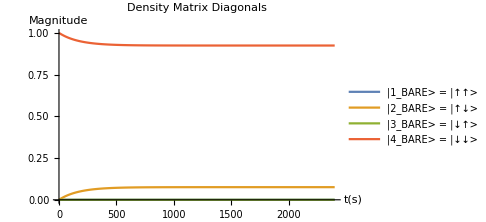
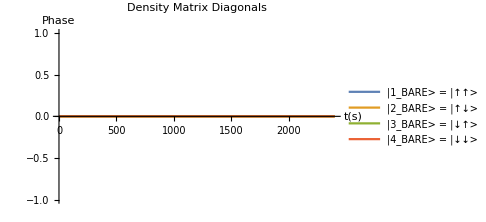

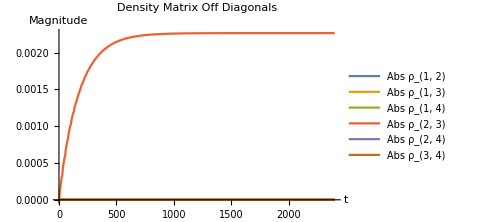
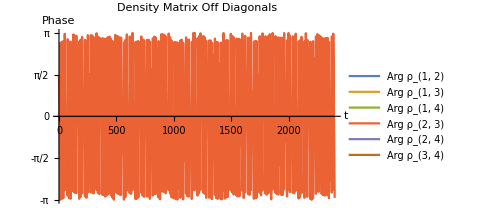

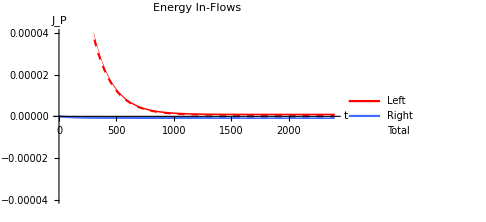

```mathematica
tmax=(1200/Subscript[ω, 1])//.Flatten[{unitassum,Tassum}];

dynamics=NDSolve[
Flatten[{sol//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}],Table[Subscript[ρ, i,j][0]==i,j i,4 1,{i,1,4},{j,1,4}]}]
,Flatten[Table[Subscript[ρ, i,j],{i,1,4},{j,1,4}]],{t,0,tmax}
];

plot1=Flatten[{Table[Abs[Subscript[ρ, i,i][t]],{i,1,4}]}/.dynamics];
plot2=Flatten[{Table[Arg[Subscript[ρ, i,i][t]],{i,1,4}]}/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> {0,1},
	AxesLabel->{Style["t(s)"],Style["Magnitude"]}, 
	PlotLegends->{
		Style["|1_BARE> = |↑↑> "],
		Style["|2_BARE> = |↑↓> "],
		Style["|3_BARE> = |↓↑> "],
		Style["|4_BARE> = |↓↓> "]}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> Full,
	AxesLabel->{Style["t(s)"],Style["Phase"]}, 
	PlotLegends->{
		Style["|1_BARE> = |↑↑> "],
		Style["|2_BARE> = |↑↓> "],
		Style["|3_BARE> = |↓↑> "],
		Style["|4_BARE> = |↓↓> "]}]}

plot1=Flatten[{Abs[Subscript[ρ, 1,2][t]],Abs[Subscript[ρ, 1,3][t]],Abs[Subscript[ρ, 1,4][t]],Abs[Subscript[ρ, 2,3][t]],Abs[Subscript[ρ, 2,4][t]],Abs[Subscript[ρ, 3,4][t]]}/.dynamics];
plot2=Flatten[{Arg[Subscript[ρ, 1,2][t]],Arg[Subscript[ρ, 1,3][t]],Arg[Subscript[ρ, 1,4][t]],Arg[Subscript[ρ, 2,3][t]],Arg[Subscript[ρ, 2,4][t]],Arg[Subscript[ρ, 3,4][t]]}/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Density Matrix Off Diagonals"],
	PlotRange-> {0.000,0.00227},
	AxesLabel->{Style["t"],Style["Magnitude"]}, 
	PlotLegends->{
		Style["Abs ρ_(1, 2)"],
		Style["Abs ρ_(1, 3)"],
		Style["Abs ρ_(1, 4)"],
		Style["Abs ρ_(2, 3)"],
		Style["Abs ρ_(2, 4)"],
		Style["Abs ρ_(3, 4)"]}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Density Matrix Off Diagonals"],
	PlotRange->Full,
	AxesLabel->{"t","Phase"}, 
	Ticks->{Automatic,{-π,-π/2,0,π/2,π}},
	PlotLegends->{
		Style["Arg ρ_(1, 2)"],
		Style["Arg ρ_(1, 3)"],
		Style["Arg ρ_(1, 4)"],
		Style["Arg ρ_(2, 3)"],
		Style["Arg ρ_(2, 4)"],
		Style["Arg ρ_(3, 4)"]}]}

plot1=Flatten[{Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 1][ρMatrix[t]]+Subscript[EngyFlowIn, 2][ρMatrix[t]]}//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}]/.dynamics];
Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Energy In-Flows"],
	PlotRange->{-0.00004,0.00004},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Right","Total"},
	PlotStyle->{Red,BlueC,{White,Dashed}}]
```

1. For weak interaction strengths (small γ values), the solutions eventually become approximately steady.
2. For fully resonant case, the solutions eventually become completely steady.

## Numerically obtaining the approximate steady-state

```mathematica
varFunc[T1_,T2_,κ1_,κ2_,ω1_,ω2_,γs_,tmax_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,NBEassum,Jassum,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[κ, 1]->κ1,Subscript[κ, 2]->κ2,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}];
temp1=sol//.temp0;
temp2=NDSolve[
Flatten[{temp1,Table[Subscript[ρ, i,j][0]==i,j i,4 1,{i,1,4},{j,1,4}]}],Flatten[Table[Subscript[ρ, i,j],{i,1,4},{j,1,4}]],{t,0,tmax}];
temp3=Table[Subscript[ρ, i,j][tmax],{i,1,4},{j,1,4}]//.Flatten[temp2];
{
Re[Flatten[Table[Subscript[ρ, i,i][tmax],{i,1,4}]/.temp2]],
Re[Flatten[{Subscript[Τs, 2][1,2],Subscript[Τs, 1][1,3],Subscript[Τs, 1][2,4],Subscript[Τs, 2][3,4],Υs[2,3,tmax]}//.Flatten[{t->tmax,temp0}]/.temp2]],
Re[Flatten[{Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]]}//.Flatten[{t->tmax,temp0}]/.temp2]],
Table[Subscript[ρ, i,j][tmax],{i,1,4},{j,1,4}]//.temp2,
Re[Flatten[{Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]]}//.Flatten[{temp0}]/.temp2]]
}
]
```

```mathematica
varFunc[0.2,0.02,0.01,0.01,1.0,1.0,0.03,1200,unitassum]
```

{{0.000010201,0.00369519,0.00301775,0.993277},{1.0201×10^-7,-1.02012×10^-7,-0.0000301779,0.0000301775,0.0000302799},{0.0000302799,-0.0000302796},{{{0.000010201+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.00369519+0. ⅈ,0.+0.00100933 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.-0.00100933 ⅈ,0.00301775+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.993277+0. ⅈ}}},{0.+Re[(-0.0000760175+0. ⅈ) InterpolatingFunction[…][t]-(0.0000760175+0. ⅈ) InterpolatingFunction[…][t]+0.01 (-1.00678 InterpolatingFunction[…][t]+0.00678365 InterpolatingFunction[…][t])-0.01 (1.00678 InterpolatingFunction[…][t]-0.00678365 InterpolatingFunction[…][t])],0.+Re[(-0.000075+0. ⅈ) InterpolatingFunction[…][t]-(0.000075+0. ⅈ) InterpolatingFunction[…][t]+0.01 (-1. InterpolatingFunction[…][t]+1.92875×10^-22 InterpolatingFunction[…][t])-0.01 (1. InterpolatingFunction[…][t]-1.92875×10^-22 InterpolatingFunction[…][t])]}}

Function for drawing a state flow diagram,

```mathematica
DrawFlowGraph[label_,posx_,posy_,nodes_,rates_,ratecolors_,ratesF_,ratecolorsF_,title_,maxrate_]:=Module[{pos,psize},
psize=Dimensions[label][[1]];
pos[i_]:={posx[[i]],posy[[i]]};
Graphics[Flatten[{
{Thickness[0.0001],Arrowheads[0.03],Black,Arrow[{{1.15Min[posx],1.2Min[posy]},{1.15Min[posx],1.1Max[posy]}}]},Black,{Text[Style["Energy",FontSize->13.6,FontFamily->"Times New Roman"],{1.0Min[posx]-0.03,1.15Max[posy]}],Text[Style[title,FontSize->13.6,FontFamily->"Times New Roman"],{0,1.57Min[posy]}]},

Table[{Opacity[1],Thick,RGBColor[0.55,0.55,0.55],Disk[pos[i],0.01+0.22 √nodes[[i]]]},{i,1,psize}],
Table[
	If[rates[[i,j]]≠0 ,
		If[ ratesF[[i,j]]≠0,
			If[Abs[rates[[i,j]]]>Abs[ratesF[[i,j]]],
				{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			,
				{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			]
		,
			{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
			ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		]
	,
		If[ ratesF[[i,j]]≠0,
			{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
			ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		, Nothing]
	]
,{i,1,psize-1},{j,i+1,psize}],
Table[{Opacity[1],Black,Text[Style[label[[i]],FontSize->12],{posx[[i]]+{0,0.04,0,0.06,0.04,0,0.04,0}[[i]],posy[[i]]+{0.045,0.08,-0.05,-0.06,0.06,-0.05,-0.08,0.045}[[i]]}]},{i,1,psize}]

}], ImageSize->Medium]
]

DrawFunc[T1_,T2_,ω1_,ω2_,γs_,title_,maxrate_,var_]:=Module[{label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,temp0},temp0=Flatten[{Jassum,NBEassum,k->1,κ->1,Subscript[T, 1]-> T1,Subscript[T, 2]-> T2,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2}];label={"|1_BARE>=|↑↑>","|2_BARE>=|↑↓>","|3_BARE>=|↓↑>","|4_BARE>=|↓↓>"};posx={0,-0.4,0.4,0};posy=Diagonal[Hsys0Matrix/(ℏ ωconv)/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}]];nodes=var[[1]];rates=({{0, var[[2]][[1]], var[[2]][[2]], 0}, {0, 0, 0, var[[2]][[3]]}, {0, 0, 0, var[[2]][[4]]}, {0, 0, 0, 0}});
ratesF=({{0, 0, 0, 0}, {0, 0, var[[2]][[5]], 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});ratecolors=({{0, Blue, Red, 0}, {0, 0, 0, Red}, {0, 0, 0, Blue}, {0, 0, 0, 0}});
ratecolorsF=({{0, 0, 0, 0}, {0, 0, PurpleC, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
DrawFlowGraph[label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,title,maxrate]
]
```

Steady-state energy flows, transition rates, density matrix diagonals and energy eigenvalues, plotted for dynamically changeable bath, and system parameters,

```mathematica
Manipulate[Module[{temp1,temp2,temp3,temp4,temp5},
temp1=varFunc[T1,T2,κ1,κ2,ω1,ω2,γs,tmax,unitassum];
temp2=Table[Hsys0EVal[i],{i,1,4}]/ℏ/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}];
temp3=Table[HsysEVal[i],{i,1,4}]/ℏ/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}];
temp4=temp1[[4]];
temp5=temp1[[5]];
{
Plot[temp2,{t,0,2},
ImageSize->Medium,
PlotLegends->{"|1_BARE> = |↑↑>","|2_BARE> = |↑↓>","|3_BARE> = |↓↑>","|4_BARE> = |↓↓>"},
AxesLabel->{None,"Frequency"},
PlotRange->{-1.5ωconv/.unitassum,1.5 ωconv/.unitassum},
Ticks->{None,Automatic}],

Plot[temp3,{t,0,2},
ImageSize->Medium,
PlotLegends->{"|1_BARE> = |↑↑>","|2_BARE> = |↑↓>","|3_BARE> = |↓↑>","|4_BARE> = |↓↓>"},
AxesLabel->{None,"Frequency"},
PlotRange->{-1.5ωconv/.unitassum,1.5 ωconv/.unitassum},
Ticks->{None,Automatic}],

Table[MatrixForm[HsysEVec[i]],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}],

Plot[temp5,{t,0,tmax},
ImageSize->Medium,
PlotLabel-> Style["Energy In-Flows"],
PlotRange->{-Emax,Emax},
AxesLabel->{"t","J_P"},
PlotLegends->{"Left ","Right","Total"},
PlotStyle->{Red,BlueC,{White,Dashed}}],

DrawFunc[T1,T2,ω1,ω2,γs,
StringForm["ω_1=``, ω_2=``, γ=``",DecimalForm[ω1,{3,2}],DecimalForm[ω2,{3,2}],DecimalForm[γs,{3,2}]],Τmax,temp1],

BarChart[temp1[[3]]
,ChartLabels->{"Left ","Right"},PlotLabel->"Equilibrium energy inflow",AxesLabel->{"","J_P(J)"},ImageSize->Medium,PlotRange->{-Emax,Emax},ChartStyle->{Red,Blue}],

BarChart[temp1[[2]]
,ChartLabels->Placed[{"R |1_BARE> to |2_BARE>","L |1_BARE> to |3_BARE>","L |2_BARE> to |4_BARE>","R |3_BARE> to |4_BARE>","γ |2_BARE> to |3_BARE>"},Bottom,Rotate[#,π/2]&],PlotLabel->"Equilibrium thermal transition rate",ImageSize->Medium,ChartStyle->{Red,Blue,Blue,Red,PurpleC}],

BarChart[temp1[[1]]
,ChartLabels->{"ρ_{1, 1}","ρ_{2, 2}","ρ_{3, 3}","ρ_{4, 4}"},PlotLabel->"Equilibrium density matrix",ImageSize->Medium,PlotRange->{-0.1,1},ChartStyle->"Pastel"]
}],
Delimiter,Item["Fixed Bath Temperatures",Alignment->Center],
{{T1,0.20 Tconv},0.001 Tconv,1 Tconv},
{{T2,0.02 Tconv},0.001 Tconv,1 Tconv},
Delimiter,Item["Bath Coupling Factors",Alignment->Center],
{{κ1,0.01},0.001,2},
{{κ2,0.01},0.001,2},
Delimiter,Item["System Parameters",Alignment->Center],
{{ω1,1.0ωconv},0ωconv,2ωconv},
{{ω2,1.0ωconv},0ωconv,2ωconv},
{{γs,0.03ωconv},0.0001ωconv,0.3ωconv},
Delimiter,Item["Simulation and Display Parameters",Alignment->Center],
{{Emax,0.00005Econv},0.00001Econv,0.001Econv},
{{tmax,1200/ωconv},100/ωconv,3000/ωconv},
{{Τmax,0.001Τconv},0.0001Τconv,0.01Τconv},
ContinuousAction->False]
```

## Energy flow characteristics for different system parameters

### Energy flow under different levels of resonance

Energy flows when ω_2 is changed from below ω_1 to above ω_1, keeping γ constant,

```mathematica
PlotEngyFlowsWithω2[T1_,T2_,κ1_,κ2_,ω1s_,ω2min_,ω2max_,γs_,tmax_,ωres_,legends_,title_]:=Module[{tempx,tempy,temp},
tempx=Table[{ω2,ω2},{ω2,ω2min,ω2max,ωres}];
tempy=10^5 Table[varFunc[T1,T2,κ1,κ2,ω1s,ω2,γs,tmax,unitassum],{ω2,ω2min,ω2max,ωres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,3,i]]}],{i,1,2}];
ListPlot[temp,
	PlotRange->{{ω2min,ω2max},{-4,4}},
	ImageSize->Medium,
	AxesStyle->Directive[Darker[Gray],13.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["ω_2",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_P(10^-5)",FontFamily->"Times New Roman",FontSize->14.5]},
	Joined->True,
  PlotLabel->Style[title,FontFamily->"Times New Roman",FontSize->14.5],
	PlotStyle->{{Red},{Blue}},
	PlotLegends->legends &&{
		Style["J_L",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_R",FontFamily->"Times New Roman",FontSize->14.5]}]
]
```

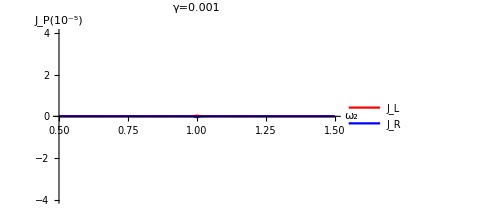
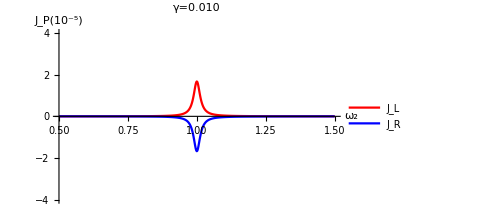
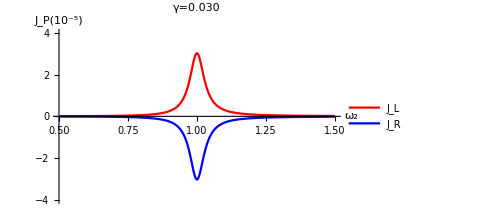

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γs=0.001ωconv;
ω1=1.0ωconv;
tmaxs=1200/ωconv;
ω2min=0.5ωconv;ω2max=1.5ωconv;ωres=0.002ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,tmaxs,ωres,True,"γ=0.001"]
],
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γs=0.01ωconv;
ω1=1.0ωconv;
tmaxs=1200/ωconv;
ω2min=0.5ωconv;ω2max=1.5ωconv;ωres=0.002ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,tmaxs,ωres,True,"γ=0.010"]
],
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γs=0.03ωconv;
ω1=1.0ωconv;
tmaxs=1200/ωconv;
ω2min=0.5ωconv;ω2max=1.5ωconv;ωres=0.002ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,tmaxs,ωres,True,"γ=0.030"]
]
}
```

### Energy flow under different levels of resonance and different coupling strengths

```mathematica
PlotEngyFlowsWithω2andγ[T1_,T2_,κ1_,κ2_,ω1s_,ω2min_,ω2max_,γmin_,γmax_,tmax_,ωres_,γres_,legends_]:=Module[{tempx,tempy,tempz,temp},
tempx=Table[ω2,{ω2,ω2min,ω2max,ωres},{γ,γmin,γmax,γres}];
tempy=Table[γ,{ω2,ω2min,ω2max,ωres},{γ,γmin,γmax,γres}];
tempz=10^5 Table[varFunc[T1,T2,κ1,κ2,ω1s,ω2,γ,tmax,unitassum][[3,1]],{ω2,ω2min,ω2max,ωres},{γ,γmin,γmax,γres}];
temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[tempz][[;;]]}];
Show[
ListPlot3D[temp,
	PlotRange->{{ω2min,ω2max},{γmin,γmax},Full},
	ImageSize->Large,
	AxesStyle->Directive[Darker[Gray],18.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["ω_2/Δ",FontFamily->"Times New Roman",FontSize->19.5],
		Style["γ/Δ",FontFamily->"Times New Roman",FontSize->19.5]},
	ColorFunction->"BlueGreenYellow"],
Graphics3D[Text[Style["10^-5J_1/ℏΔ^2",Darker[Gray],FontFamily->"Times New Roman",FontSize->19.5],Scaled[{0.13,0.03,0.72}]]]
]
]
```

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,γmin,γmax,tmaxs,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.001ωconv;γmax=0.03 ωconv;γres=0.0015;
ω1=1.0ωconv;
tmaxs=1200/ωconv;
ω2min=0.8ωconv;ω2max=1.2ωconv;ωres=0.001ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ω2min,ω2max,γmin,γmax,tmaxs,ωres,γres,True]
]
```

-Graphics3D-